csv plotter

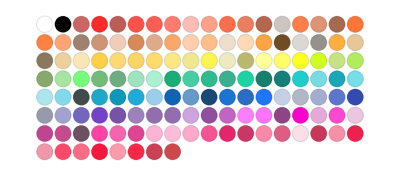

```mathematica
ColorData["Crayola","Panel"]
```

#### csv 1

```mathematica
CSVnOnly = Import["C:\\Users\\ferin\\Dropbox\\_cooperate\\ABM-PDE-master\\csv\\no-delay\\concentrations-N-only.csv"];
```

```mathematica
CSVrn = Import["C:\\Users\\ferin\\Dropbox\\_cooperate\\ABM-PDE-master\\csv\\no-delay\\concentrations-RN.csv"];
```

```mathematica
Only1 =Flatten[CSVnOnly[[All,{1}]]];
Only2 =Flatten[CSVnOnly[[All,{2}]]];
Only3 =Flatten[CSVnOnly[[All,{3}]]];
```

```mathematica
csvPlotNoDelayLeft=ListPlot[{Only1, Only2, Only3},
Frame->{True,True,False,False},
Joined->True,
Axes->False,
Mesh->Full,
PlotStyle->{{Directive[ColorData["Crayola","Cerulean"]], Thickness[0.005]},{Directive[ColorData["Crayola","LemonYellow"]], Thickness[0.01]},{Directive[ColorData["Crayola","Plum"]], Thickness[0.005]}},
PlotTheme->"Scientific",
FrameTicks->{{Drop[Range[0,20000,5000], 1],None},{Range[0, 8000, 2000], None}},
PlotRange->{{0,8000},{0,20000}},
LabelStyle->Directive[FontFamily->"Times",Black,FontSize->28],
ImageSize->{800, 500},
 GridLines->None];
```

```mathematica
fOnly2 = Interpolation[Transpose[{Range[0, Length[Only2]-1, 1], Only2}]];
fOnly3 = Interpolation[Transpose[{Range[0, Length[Only3]-1, 1], Only3}], InterpolationOrder->2];
```

```mathematica
commonPadding = {{100, 100},{100, 10}}
```

{{100,100},{100,10}}

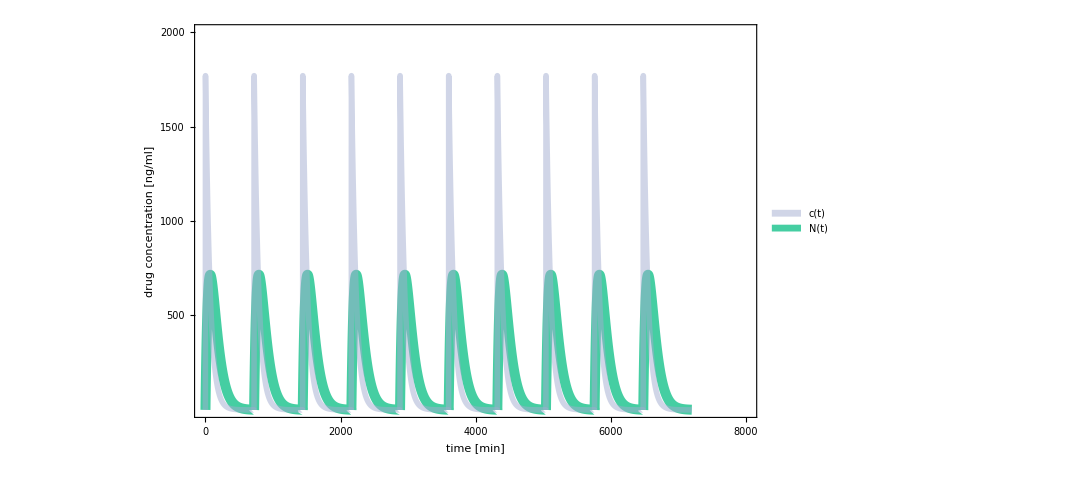

```mathematica
CentralColor = "WildBlueYonder";
LungColor = "Shamrock";
csvPlotNoDelayLeftA=Legended[Plot[{fOnly2[t], Min[fOnly3[t],1770]},
{t, 0, Length[Only2]-1},
Exclusions->None,
PlotPoints->10000,
Frame->{{True,False},{True,False}},
Axes->False,
PlotStyle->{{Directive[ColorData["Crayola",LungColor]], Thickness[0.009]},{Directive[ColorData["Crayola",CentralColor]], Thickness[0.005], Opacity[.5]}},
PlotTheme->"Scientific",
FrameTicks->{{Drop[Range[0,2000,500], 1],None},{Range[0, 8000, 2000], None}},
FrameLabel->{{Style["drug concentration [ng/ml]", ColorData["Crayola","Black"], 26], None},{Style["time [min]", ColorData["Crayola","Black"], 26], None}},
PlotRange->{{0,8000},{0,2000}},
LabelStyle->Directive[FontFamily->"Times",Black,FontSize->28],
ImageSize->{800, 500},
ImagePadding->commonPadding,
 GridLines->None],
Placed[SwatchLegend[{{ColorData["Crayola",CentralColor], Opacity[.5]}, ColorData["Crayola",LungColor]},{"c(t)","N(t)"},LabelStyle->{FontFamily->"Times",FontSize->26}],{0.9,0.9}]]
```

```mathematica
fOnly1 = Interpolation[Transpose[{Range[0, Length[Only1]-1, 1], Only1}]];
```

```mathematica
axisLabel = Grid[{{Style["- -", ColorData["Crayola",VirusColor], 10],Style["virus concentration [copies/ml]", ColorData["Crayola",VirusColor], 26]}}, Alignment->{Center, Center}]
```

- - | virus concentration [copies/ml]

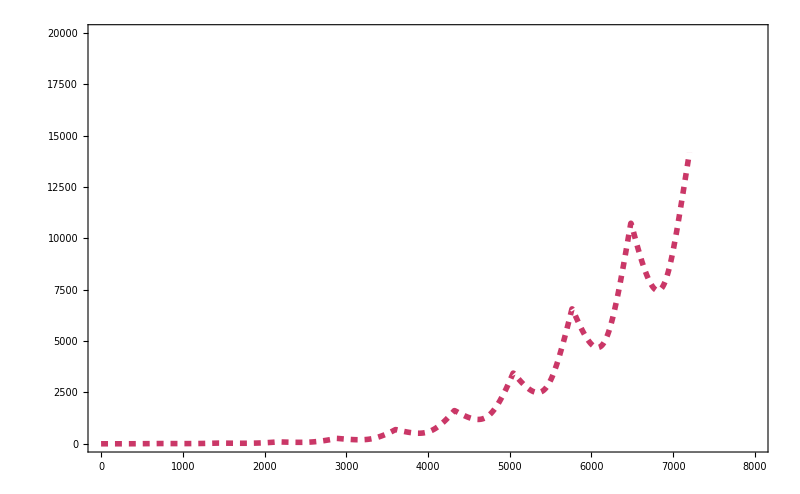

```mathematica
VirusColor = "JazzberryJam";
csvPlotNoDelayLeftB=Plot[{fOnly1[t]},
{t, 0, Length[Only1]-1},
Frame->{{False,True},{False,False}},
PlotStyle->{{Directive[ColorData["Crayola",VirusColor]], Thickness[0.005], Dashed},{Directive[ColorData["Crayola","LemonYellow"]], Thickness[0.01]},{Directive[ColorData["Crayola","Plum"]], Thickness[0.005]}},
PlotTheme->"Scientific",
FrameTicks->{{None,Drop[Range[0,20000,5000], 1]},{None,None}},
FrameTicksStyle->Directive[ColorData["Crayola",VirusColor],20],
FrameLabel->{{None,axisLabel},{None, None}},
PlotRange->{{0,8000},{0,20000}},
LabelStyle->Directive[FontFamily->"Times",Black,FontSize->28],
ImagePadding->commonPadding,
ImageSize->{800, 500},
 GridLines->None]
```

```mathematica
Overlay[{csvPlotNoDelayLeftA, csvPlotNoDelayLeftB}]
Export["2_nirm_only.pdf",%]
```

-Graphics--Graphics-

2_nirm_only.pdf

```mathematica
Only1b =Flatten[CSVrn[[All,{1}]]];
Only2b =Flatten[CSVrn[[All,{2}]]];
Only3b =Flatten[CSVrn[[All,{3}]]];
```

```mathematica
csvPlotNoDelayRight=ListPlot[{Only1b, Only2b, Only3b},
Frame->{True,True,False,False},
Joined->True,
Axes->False,
Mesh->Full,
PlotStyle->{{Directive[ColorData["Crayola","Cerulean"]], Thickness[0.005]},{Directive[ColorData["Crayola","LemonYellow"]], Thickness[0.01]},{Directive[ColorData["Crayola","Plum"]], Thickness[0.005]}},
PlotTheme->"Scientific",
FrameTicks->{{Drop[Range[0,8000,2000], 1],None},{Range[0, 8000, 2000], None}},
PlotRange->{{0,8000},{0,8000}},
LabelStyle->Directive[FontFamily->"Times",Black,FontSize->28],
ImageSize->{800, 500},
 GridLines->None];
```

```mathematica
fOnly2b = Interpolation[Transpose[{Range[0, Length[Only2b]-1, 1], Only2b}]];
fOnly3b = Interpolation[Transpose[{Range[0, Length[Only3b]-1, 1], Only3b}], InterpolationOrder->10];
```

```mathematica
commonPadding = {{100, 100},{100, 10}}
```

{{100,100},{100,10}}

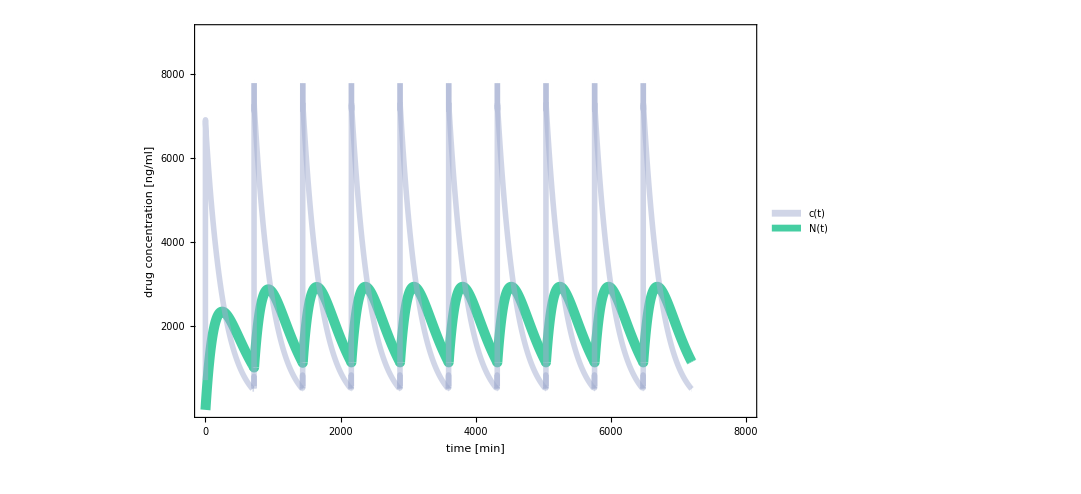

```mathematica
CentralColor = "WildBlueYonder";
LungColor = "Shamrock";
csvPlotNoDelayRightA=Legended[Plot[{fOnly2b[t], Min[Max[fOnly3b[t], 500], 7800]},
{t, 0, Length[Only2b]-1},
PlotPoints->10000,
Frame->{{True,False},{True,False}},
Axes->False,
PlotStyle->{{Directive[ColorData["Crayola",LungColor]], Thickness[0.009]},{Directive[ColorData["Crayola",CentralColor]], Thickness[0.005], Opacity[.5]}},
PlotTheme->"Scientific",
FrameTicks->{{Drop[Range[0,8000,2000], 1],None},{Range[0, 8000, 2000], None}},
FrameLabel->{{Style["drug concentration [ng/ml]", ColorData["Crayola","Black"], 26], None},{Style["time [min]", ColorData["Crayola","Black"], 26], None}},
PlotRange->{{0,8000},{0,9000}},
LabelStyle->Directive[FontFamily->"Times",Black,FontSize->28],
ImageSize->{800, 500},
ImagePadding->commonPadding,
 GridLines->None],
Placed[SwatchLegend[{{ColorData["Crayola",CentralColor], Opacity[.5]}, ColorData["Crayola",LungColor]},{"c(t)","N(t)"},LabelStyle->{FontFamily->"Times",FontSize->26}],{0.9,0.9}]]
```

```mathematica
fOnly1b = Interpolation[Transpose[{Range[0, Length[Only1b]-1, 1], Only1b}]];
```

```mathematica
axisLabel = Grid[{{Style["- -", ColorData["Crayola",VirusColor], 10],Style["virus concentration [copies/ml]", ColorData["Crayola",VirusColor], 26]}}, Alignment->{Center, Center}]
```

- - | virus concentration [copies/ml]

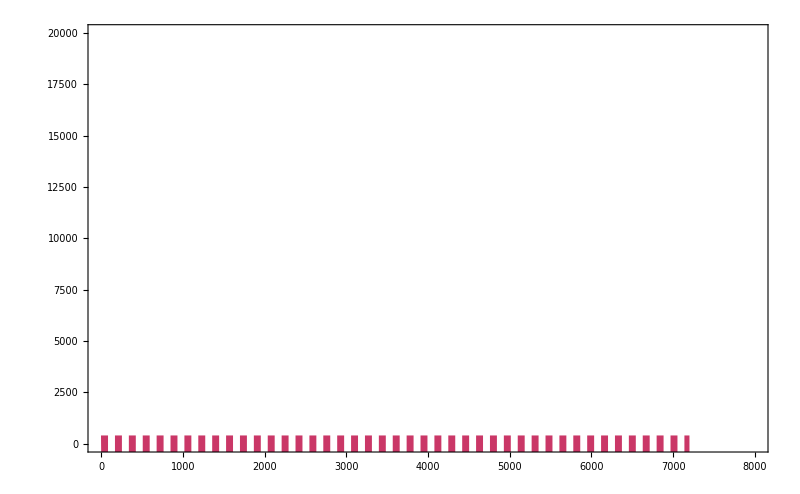

```mathematica
VirusColor = "JazzberryJam";
csvPlotNoDelayRightB=Plot[{fOnly1b[t]},
{t, 0, Length[Only1b]-1},
Frame->{{False,True},{False,False}},
PlotStyle->{{Directive[ColorData["Crayola",VirusColor]], Thickness[0.015], Dashed},{Directive[ColorData["Crayola","LemonYellow"]], Thickness[0.01]},{Directive[ColorData["Crayola","Plum"]], Thickness[0.005]}},
PlotTheme->"Scientific",
FrameTicks->{{None,Drop[Range[0,20000,5000], 1]},{None,None}},
FrameTicksStyle->Directive[ColorData["Crayola",VirusColor],20],
FrameLabel->{{None,axisLabel},{None, None}},
PlotRange->{{0,8000},{0,20000}},
LabelStyle->Directive[FontFamily->"Times",Black,FontSize->28],
ImagePadding->commonPadding,
ImageSize->{800, 500},
 GridLines->None]
```

```mathematica
Overlay[{csvPlotNoDelayRightA, csvPlotNoDelayRightB}]
Export["3_RN.pdf",%]
```

-Graphics--Graphics-

3_RN.pdf

#### csv 2

```mathematica
CSVnOnly2 = Import["C:\\Users\\ferin\\Dropbox\\_cooperate\\ABM-PDE-master\\csv\\36h-delay\\concentrationsN-o.csv"];
```

```mathematica
CSVrn2 = Import["C:\\Users\\ferin\\Dropbox\\_cooperate\\ABM-PDE-master\\csv\\36h-delay\\concentrationsRN.csv"];
```

```mathematica
Only12 =Flatten[CSVnOnly2[[All,{1}]]];
Only22 =Flatten[CSVnOnly2[[All,{2}]]];
Only32 =Flatten[CSVnOnly2[[All,{3}]]];
```

```mathematica
csvPlot36DelayLeft=ListPlot[{Only12, Only22, Only32},
Frame->{True,True,False,False},
Joined->True,
Axes->False,
Mesh->Full,
PlotStyle->{{Directive[ColorData["Crayola","Cerulean"]], Thickness[0.005]},{Directive[ColorData["Crayola","LemonYellow"]], Thickness[0.01]},{Directive[ColorData["Crayola","Plum"]], Thickness[0.005]}},
PlotTheme->"Scientific",
FrameTicks->{{Drop[Range[0,20000,5000], 1],None},{Range[0, 10000, 2000], None}},
PlotRange->{{0,10000},{0,20000}},
LabelStyle->Directive[FontFamily->"Times",Black,FontSize->28],
ImageSize->{800, 500},
 GridLines->None];
```

```mathematica
fOnly22 = Interpolation[Transpose[{Range[0, Length[Only22]-1, 1], Only22}]];
fOnly32 = Interpolation[Transpose[{Range[0, Length[Only32]-1, 1], Only32}], InterpolationOrder->2];
```

```mathematica
commonPadding = {{100, 100},{100, 10}}
```

{{100,100},{100,10}}

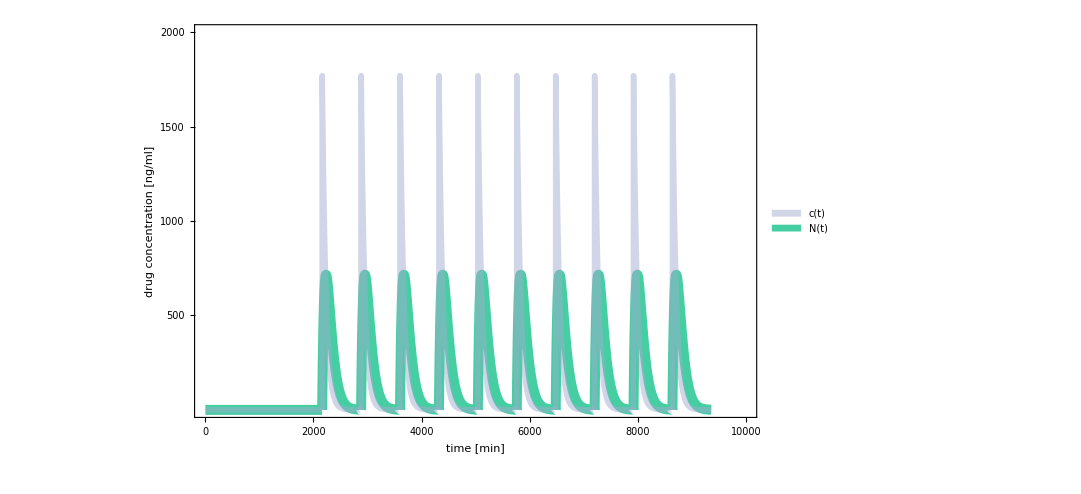

```mathematica
CentralColor = "WildBlueYonder";
LungColor = "Shamrock";
csvPlot36DelayLeftA=Legended[Plot[{fOnly22[t], Min[fOnly32[t],1770]},
{t, 0, Length[Only22]-1},
Exclusions->None,
PlotPoints->10000,
Frame->{{True,False},{True,False}},
Axes->False,
PlotStyle->{{Directive[ColorData["Crayola",LungColor]], Thickness[0.009]},{Directive[ColorData["Crayola",CentralColor]], Thickness[0.005], Opacity[.5]}},
PlotTheme->"Scientific",
FrameTicks->{{Drop[Range[0,2000,500], 1],None},{Range[0, 10000, 2000], None}},
FrameLabel->{{Style["drug concentration [ng/ml]", ColorData["Crayola","Black"], 26], None},{Style["time [min]", ColorData["Crayola","Black"], 26], None}},
PlotRange->{{0,10000},{0,2000}},
LabelStyle->Directive[FontFamily->"Times",Black,FontSize->28],
ImageSize->{800, 500},
ImagePadding->commonPadding,
 GridLines->None],
Placed[SwatchLegend[{{ColorData["Crayola",CentralColor], Opacity[.5]}, ColorData["Crayola",LungColor]},{"c(t)","N(t)"},LabelStyle->{FontFamily->"Times",FontSize->26}],{0.9,0.9}]]
```

```mathematica
fOnly12 = Interpolation[Transpose[{Range[0, Length[Only12]-1, 1], Only12}]];
```

```mathematica
axisLabel = Grid[{{Style["- -", ColorData["Crayola",VirusColor], 10],Style["virus concentration [copies/ml]", ColorData["Crayola",VirusColor], 26]}}, Alignment->{Center, Center}]
```

- - | virus concentration [copies/ml]

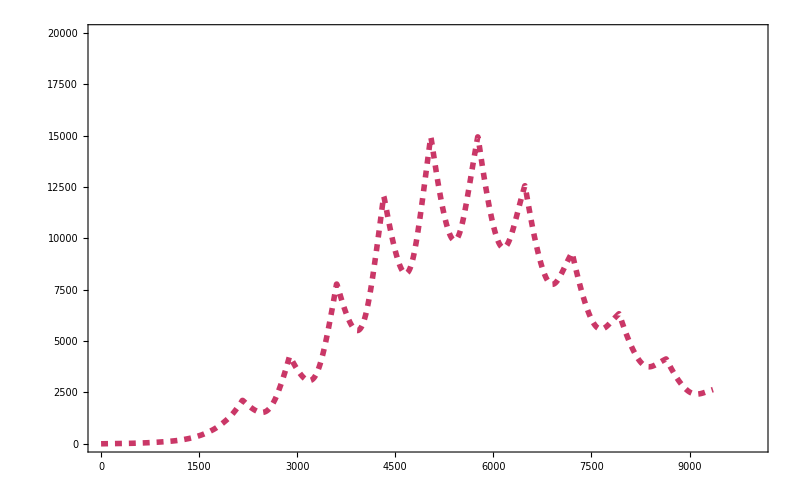

```mathematica
VirusColor = "JazzberryJam";
csvPlot36DelayLeftB=Plot[{fOnly12[t]},
{t, 0, Length[Only12]-1},
Frame->{{False,True},{False,False}},
PlotStyle->{{Directive[ColorData["Crayola",VirusColor]], Thickness[0.005], Dashed},{Directive[ColorData["Crayola","LemonYellow"]], Thickness[0.01]},{Directive[ColorData["Crayola","Plum"]], Thickness[0.005]}},
PlotTheme->"Scientific",
FrameTicks->{{None,Drop[Range[0,20000,5000], 1]},{None,None}},
FrameTicksStyle->Directive[ColorData["Crayola",VirusColor],20],
FrameLabel->{{None,axisLabel},{None, None}},
PlotRange->{{0,10000},{0,20000}},
LabelStyle->Directive[FontFamily->"Times",Black,FontSize->28],
ImagePadding->commonPadding,
ImageSize->{800, 500},
 GridLines->None]
```

```mathematica
Overlay[{csvPlot36DelayLeftA, csvPlot36DelayLeftB}]
Export["nirmatrelvir_only_36h_delay.pdf",%]
```

-Graphics--Graphics-

nirmatrelvir_only_36h_delay.pdf

```mathematica
Only1b2 =Flatten[CSVrn2[[All,{1}]]];
Only2b2 =Flatten[CSVrn2[[All,{2}]]];
Only3b2 =Flatten[CSVrn2[[All,{3}]]];
```

```mathematica
csvPlot36DelayRight=ListPlot[{Only1b2, Only2b2, Only3b2},
Frame->{True,True,False,False},
Joined->True,
Axes->False,
Mesh->Full,
PlotStyle->{{Directive[ColorData["Crayola","Cerulean"]], Thickness[0.005]},{Directive[ColorData["Crayola","LemonYellow"]], Thickness[0.01]},{Directive[ColorData["Crayola","Plum"]], Thickness[0.005]}},
PlotTheme->"Scientific",
FrameTicks->{{Drop[Range[0,8000,2000], 1],None},{Range[0, 10000, 2000], None}},
PlotRange->{{0,10000},{0,8000}},
LabelStyle->Directive[FontFamily->"Times",Black,FontSize->28],
ImageSize->{800, 500},
 GridLines->None];
```

```mathematica
fOnly2b2 = Interpolation[Transpose[{Range[0, Length[Only2b2]-1, 1], Only2b2}]];
fOnly3b2 = Interpolation[Transpose[{Range[0, Length[Only3b2]-1, 1], Only3b2}], InterpolationOrder->10];
```

```mathematica
commonPadding = {{100, 100},{100, 10}}
```

{{100,100},{100,10}}

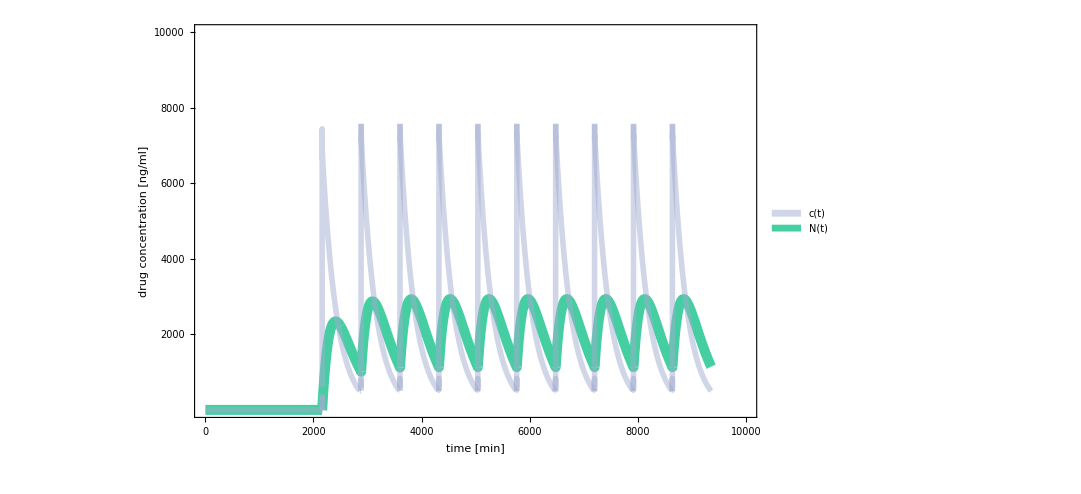

```mathematica
CentralColor = "WildBlueYonder";
LungColor = "Shamrock";
csvPlot36DelayRightA=Legended[Plot[{fOnly2b2[t], Min[If[t<2500,fOnly3b2[t],Max[fOnly3b2[t], 500]], 7600]},
{t, 0, Length[Only2b2]-1},
PlotPoints->10000,
Frame->{{True,False},{True,False}},
Axes->False,
PlotStyle->{{Directive[ColorData["Crayola",LungColor]], Thickness[0.009]},{Directive[ColorData["Crayola",CentralColor]], Thickness[0.005], Opacity[.5]}},
PlotTheme->"Scientific",
FrameTicks->{{Drop[Range[0,10000,2000], 1],None},{Range[0, 10000, 2000], None}},
FrameLabel->{{Style["drug concentration [ng/ml]", ColorData["Crayola","Black"], 26], None},{Style["time [min]", ColorData["Crayola","Black"], 26], None}},
PlotRange->{{0,10000},{0,10000}},
LabelStyle->Directive[FontFamily->"Times",Black,FontSize->28],
ImageSize->{800, 500},
ImagePadding->commonPadding,
 GridLines->None],
Placed[SwatchLegend[{{ColorData["Crayola",CentralColor], Opacity[.5]}, ColorData["Crayola",LungColor]},{"c(t)","N(t)"},LabelStyle->{FontFamily->"Times",FontSize->26}],{0.9,0.9}]]
```

```mathematica
fOnly1b2 = Interpolation[Transpose[{Range[0, Length[Only1b2]-1, 1], Only1b2}]];
```

```mathematica
axisLabel = Grid[{{Style["- -", ColorData["Crayola",VirusColor], 10],Style["virus concentration [copies/ml]", ColorData["Crayola",VirusColor], 26]}}, Alignment->{Center, Center}]
```

- - | virus concentration [copies/ml]

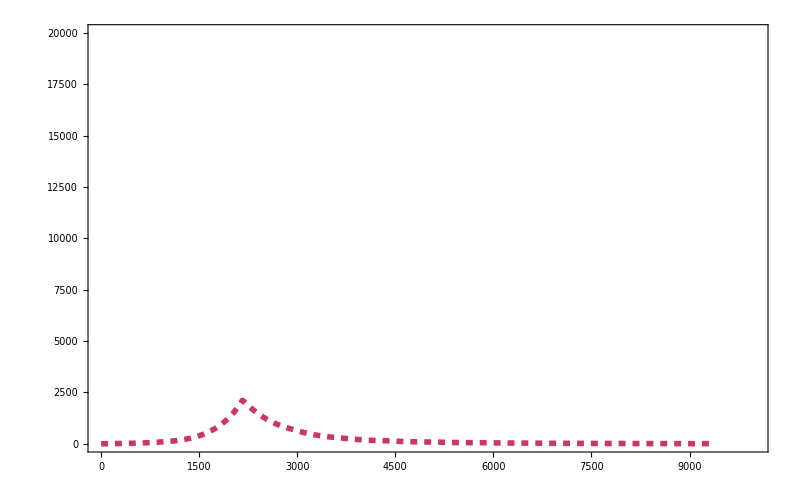

```mathematica
VirusColor = "JazzberryJam";
csvPlot36DelayRightB=Plot[{fOnly1b2[t]},
{t, 0, Length[Only1b2]-1},
Frame->{{False,True},{False,False}},
PlotStyle->{{Directive[ColorData["Crayola",VirusColor]], Thickness[0.005], Dashed},{Directive[ColorData["Crayola","LemonYellow"]], Thickness[0.005]},{Directive[ColorData["Crayola","Plum"]], Thickness[0.005]}},
PlotTheme->"Scientific",
FrameTicks->{{None,Drop[Range[0,20000,5000], 1]},{None,None}},
FrameTicksStyle->Directive[ColorData["Crayola",VirusColor],20],
FrameLabel->{{None,axisLabel},{None, None}},
PlotRange->{{0,10000},{0,20000}},
LabelStyle->Directive[FontFamily->"Times",Black,FontSize->28],
ImagePadding->commonPadding,
ImageSize->{800, 500},
 GridLines->None]
```

```mathematica
Overlay[{csvPlot36DelayRightA, csvPlot36DelayRightB}]
Export["rito_nirm_36h_delay.pdf",%]
```

-Graphics--Graphics-

rito_nirm_36h_delay.pdf